```mathematica
(* Problem #4 *)
```

```mathematica
Quit[]
```

```mathematica
(*
Symbols;
q1: joint angle of link1;
q2: joint angle of link2;
q3: x of ball;
q4: y of ball;
*)
qall={{q1[t],q2[t],q3[t],q4[t]}};
```

```mathematica
(* Double Pendulum Kinematics *)
m1=1;m2=1;R1=1;R2=1;
g=9.8;
x1=R1 Cos[q1[t]];
y1=R1 Sin[q1[t]];
x2=x1+R2 Cos[q1[t]+q2[t]];
y2=y1+R2 Sin[q1[t]+q2[t]];
vx1=D[x1,t];vy1=D[y1,t];
vx2=D[x2,t];vy2=D[y2,t];
LagPendulum=1/2 m1 (vx1^2+vy1^2)+1/2 m2 (vx2^2+vy2^2)-m1 g y1-m2 g y2//FullSimplify;

(*Ball Kinematics*)
M=1;
g2=2;
LagBALL=1/2*M*(q3'[t]^2+q4'[t]^2)-M*g2*q4[t];

(*E-L Eqs*)
Lag=LagPendulum+LagBALL;
Eq1=D[D[Lag,q1'[t]],t]-D[Lag,q1[t]]//FullSimplify;
Eq2=D[D[Lag,q2'[t]],t]-D[Lag,q2[t]]//FullSimplify;
Eq3=D[D[Lag,q3'[t]],t]-D[Lag,q3[t]]//FullSimplify;
Eq4=D[D[Lag,q4'[t]],t]-D[Lag,q4[t]]//FullSimplify;
```

```mathematica
(* Solve motion when there is no impact*)
EQ=Solve[{Eq1==0,Eq2==0,Eq3==0,Eq4==0},
{q1''[t],q2''[t],q3''[t],q4''[t]}];
Print["-------------------------\nSolve for q1~q4:"]
Print[EQ[[1,1]],"\n",EQ[[1,2]],"\n",EQ[[1,3]],"\n",EQ[[1,4]]]
```

-------------------------
Solve for q1~q4:

q1''[t]→-1/(-2.+Cos[q2[t]]^2)9.8 (0.-2. Cos[q1[t]]+1. Cos[q2[t]] Cos[q1[t]+q2[t]]+0.102041 Sin[q2[t]] q1'[t]^2+0.102041 Cos[q2[t]] Sin[q2[t]] q1'[t]^2+0.204082 Sin[q2[t]] q1'[t] q2'[t]+0.102041 Sin[q2[t]] q2'[t]^2)
q2''[t]→1/(-2.+Cos[q2[t]]^2)9.8 (-2. Cos[q1[t]]-2. Cos[q1[t]] Cos[q2[t]]+2. Cos[q1[t]+q2[t]]+1. Cos[q2[t]] Cos[q1[t]+q2[t]]+0.306122 Sin[q2[t]] q1'[t]^2+0.204082 Cos[q2[t]] Sin[q2[t]] q1'[t]^2+0.204082 Sin[q2[t]] q1'[t] q2'[t]+0.204082 Cos[q2[t]] Sin[q2[t]] q1'[t] q2'[t]+0.102041 Sin[q2[t]] q2'[t]^2+0.102041 Cos[q2[t]] Sin[q2[t]] q2'[t]^2)
q3''[t]→0.
q4''[t]→-2.

```mathematica
(*Impact conditions*)

(*Link1 impact with the ball*)
(*Impact surface: Tan[q1]*(x[t]-link1x0)=(y[t]-link1y0)*)
ϕlink1ball=Sin[q1[t]]*(q3[t]-0)-Cos[q1[t]]*(q4[t]-0);
dϕlink1ball=D[ϕlink1ball,qall];
surfaceϕlink1ball[qq1_,qq2_,qq3_,qq4_]:=ϕlink1ball/.{q1[t]->qq1,q2[t]->qq2,q3[t]->qq3,q4[t]->qq4};

(*Link2 impact with the ball*)
(*Impact surface: Tan[qsum]*(x[t]-link2x0)=(y[t]-link2y0)*)
qsum=q1[t]+q2[t];
link2x0=R1*Cos[q1[t]];
link2y0=R1*Sin[q1[t]];
ϕlink2ball=Sin[qsum]*(q3[t]-link2x0)-Cos[qsum]*(q4[t]-link2y0);
dϕlink2ball=D[ϕlink2ball,qall];
surfaceϕlink2ball[qq1_,qq2_,qq3_,qq4_]:=ϕlink2ball/.{q1[t]->qq1,q2[t]->qq2,q3[t]->qq3,q4[t]->qq4};

(*Ball impact with the walls on bottom, up, right, left*)
lensquare=2; (*length of the squared-shaped wall*)

ϕwalldown=q4[t]+lensquare;
dϕwalldown=D[ϕwalldown,qall];
surfaceϕwalldown[qq3_,qq4_]:=ϕwalldown/.{q1[t]->qq1,q2[t]->qq2,q3[t]->qq3,q4[t]->qq4};

ϕwallup=q4[t]-lensquare;
dϕwallup=D[ϕwallup,qall];
surfaceϕwallup[qq3_,qq4_]:=ϕwallup/.{q1[t]->qq1,q2[t]->qq2,q3[t]->qq3,q4[t]->qq4};

ϕwallright=q3[t]-lensquare;
dϕwallright=D[ϕwallright,qall];
surfaceϕwallright[qq3_,qq4_]:=ϕwallright/.{q1[t]->qq1,q2[t]->qq2,q3[t]->qq3,q4[t]->qq4};

ϕwallleft=q3[t]+lensquare;
dϕwallleft=D[ϕwallleft,qall];
surfaceϕwallleft[qq3_,qq4_]:=ϕwallleft/.{q1[t]->qq1,q2[t]->qq2,q3[t]->qq3,q4[t]->qq4};

(*Link2 impact with the x=0 wall*)
ϕwallverticle=x2;
dϕwallverticle=D[ϕwallverticle,qall];
surfaceϕwallverticle[qq1_,qq2_]:=ϕwallverticle/.{q1[t]->qq1,q2[t]->qq2,q3[t]->qq3,q4[t]->qq4};
```

```mathematica
(* Assistive functions*)

(*return the distance between p1 and p2*)
CalcDist[x1_,y1_,x2_,y2_]:=Sqrt[(x2-x1)^2+(y2-y1)^2];

(* return the angle between (pb,p0) and (pb,p1) *)
CosLaw[x0_,y0_,x1_,y1_,xb_,yb_]:=Module[
{a,b,c,costheta},
a=CalcDist[xb,yb,x0,y0];
       b=CalcDist[xb,yb,x1,y1];
c=CalcDist[x0,y0,x1,y1];
costheta=(a^2+b^2-c^2)/(2*a*b);
ArcCos[costheta]
];

myArcTan[x0_,y0_,x1_,y1_]:=ArcTan[y1-y0,x1-x0];
myPiToPi[theta_]:=Which[theta>Pi,theta-2*Pi,theta<-Pi,theta+2*Pi,True,theta];

(*Check if the projection of pb=(xb,yb) is in the line of p0~p1*)
isInLine[x0_,y0_,x1_,y1_,xb_,yb_]:=Module[
{dx,dy,innerproduct},
dx=x1-x0;
dy=y1-y0;
innerproduct=(xb-x0)*dx+(yb-y0)*dy;
0≤innerproduct&&innerproduct≤dx*dx+dy*dy
];
If[False,
Print["Test funcs:",
"\n",CalcDist[0,0,1,0],
"\n",CosLaw[0,0,1,0,0.5,0.2],
"\n",isInLine[0,0,1,0,0.5,0.2]]];
```

```mathematica
(*Detect impact events, assign value to dϕdqall if an impact is detected*)
DetectImpactEvents[qq1_,qq2_,qq3_,qq4_]:=Module[{x0,y0,x1,y1,x2,y2,xb,yb},
x0=0;y0=0;(*axis of link 1*)
x1=x0+R1*Cos[qq1];
y1=y0+R1*Sin[qq1];(*axis of link 2*)
x2=x1+R2*Cos[qq1+qq2];
y2=y1+R2*Cos[qq1+qq2];
xb=qq3;
yb=qq4;
(* Detect impact events*)
(* I put all impact events inside "Which" *)
FlagNoImpact=0;
Which[
(* Ball~walls*)
surfaceϕwalldown[qq3,qq4]<0,(dϕdqall=dϕwalldown),
surfaceϕwallup[qq3,qq4]>0,(dϕdqall=dϕwallup),
surfaceϕwallright[qq3,qq4]>0,(dϕdqall=dϕwallright),
surfaceϕwallleft[qq3,qq4]<0,(dϕdqall=dϕwallleft),

(*This is just a test*)
(*surfaceϕwallverticle[qq1,qq2]>0,(dϕdqall=dϕwallverticle;FlagNoImpact=0),*)

(*Ball~Link1*)
isInLine[x0,y0,x1,y1,xb,yb]&&Abs[surfaceϕlink1ball[qq1,qq2,qq3,qq4]]<impactDetectionError,
(dϕdqall=dϕlink1ball),

(*Ball~Link2*)
isInLine[x1,y1,x2,y2,xb,yb]&&Abs[surfaceϕlink2ball[qq1,qq2,qq3,qq4]]<impactDetectionError,
(dϕdqall=dϕlink2ball),

True,FlagNoImpact=1 (*No impact detected*)
];
FlagNoImpact (* Output *)
];
```

```mathematica
(* Solve motion starting from t0, until get an impact *)
(*phi[tt_]:=x3/.t->tt;*)
OneBounce[{t0_,q10_,dq10_,q20_,dq20_,q30_,dq30_,q40_,dq40_}]:=
Module[
{sol,t1,
q11,dq11,q21,dq21,q31,dq31,q41,dq41},
FlagNoImpact=1;
sol=First[NDSolve[
{q1''[t]==EQ[[1,1,2]],
q2''[t]==EQ[[1,2,2]],
q3''[t]==EQ[[1,3,2]],
q4''[t]==EQ[[1,4,2]],
q1[t0]==q10,q1'[t0]==dq10,
q2[t0]==q20,q2'[t0]==dq20,
q3[t0]==q30,q3'[t0]==dq30,
q4[t0]==q40,q4'[t0]==dq40},
{q1,q2,q3,q4},{t,t0,T},
(*------------------------------Impact Conditions-------------------------------*)
Method->{"EventLocator",
"Event":>{
DetectImpactEvents[q1[t],q2[t],q3[t],q4[t]]
},"EventAction":>(Throw[end=t,"StopIntegration"])
},MaxStepSize->intergrationMaxStepSize]];

(*Reflection*)
t1=(q1/.sol)[[1,-1,2]];(*current time*)
qBeforeImpact={q1[t1],q1'[t1],q2[t1],q2'[t1],q3[t1],q3'[t1],q4[t1],q4'[t1]}/.sol;
{q11,dq11,q21,dq21,q31,dq31,q41,dq41}=If[FlagNoImpact==1,qBeforeImpact,
(*if there is an impact:*)Reflection[dϕdqall][qBeforeImpact]];

(*Print result*)
If[ifprint,Print["Impact detected at: t=",t1,",impactcase=",impactcase]];
If[ifprint,Print["    Before reflection, q=:",qBeforeImpact]];
If[ifprint,Print["    After reflection",{q11,dq11,q21,dq21}]];

(* Sow the output*)
Sow[{{q1[t],q2[t],q3[t],q4[t]}/.sol,t0≤t≤t1},"qhist"];
Sow[{{q1[t]}/.sol,t0≤t≤t1},"q1hist"];
Sow[{{q2[t]}/.sol,t0≤t≤t1},"q2hist"];
Sow[{{q3[t]}/.sol,t0≤t≤t1},"q3hist"];
Sow[{{q4[t]}/.sol,t0≤t≤t1},"q4hist"];
Sow[{q11,q21,q31,q41},"Bounces"];
{t1,q11,dq11,q21,dq21,q31,dq31,q41,dq41}
]
```

```mathematica
(* Do simulations until end=T *)
BouncingBall[{q1_,dq1_,q2_,dq2_,q3_,dq3_,q4_,dq4_}]:=Module[{data,end,bounces},
data=Reap[Catch[NestWhile[OneBounce,{0,q1,dq1,q2,dq2,q3,dq3,q4,dq4},Function[#1[[1]]<T],1,maxbouncing]],_,Rule];
end=data[[1,1]];
data=Last[data];
bounces=("Bounces"/.data);
{end,data,bounces}
]
```

```mathematica
(* The update law at impact *)
dϕ1dq1[tt_]:=D[ϕ1,q1[t]]/.t->tt;
dϕ1dq2[tt_]:=D[ϕ1,q2[t]]/.t->tt;
dϕ1dq3[tt_]:=D[ϕ1,q3[t]]/.t->tt;
dϕ1dq4[tt_]:=D[ϕ1,q4[t]]/.t->tt;
p1[tt_]:=D[Lag,q1'[t]]/.t->tt;
p2[tt_]:=D[Lag,q2'[t]]/.t->tt;
p3[tt_]:=D[Lag,q3'[t]]/.t->tt;
p4[tt_]:=D[Lag,q4'[t]]/.t->tt;
H[tt_]:=(p1[t]*q1'[t]+p2[t]*q2'[t]+p3[t]*q3'[t]+p4[t]*q4'[t]-Lag)/.t->tt;
```

```mathematica
Reflection[dϕdqall_][{q10_,dq10_,q20_,dq20_,q30_,dq30_,q40_,dq40_}]:=
Module[{q11,dq11,q21,dq21,q31,dq31,q41,dq41}(*derivatisInLine[x0,y0,x1,y1,xb,yb]&&ives*),
vars={
q1[tminus]->q10,q1'[tminus]->dq10,q1[tplus]->q11,q1'[tplus]->dq11,
q2[tminus]->q20,q2'[tminus]->dq20,q2[tplus]->q21,q2'[tplus]->dq21,
q3[tminus]->q30,q3'[tminus]->dq30,q3[tplus]->q31,q3'[tplus]->dq31,
q4[tminus]->q40,q4'[tminus]->dq40,q4[tplus]->q41,q4'[tplus]->dq41
};
q11=q10;
q21=q20;
q31=q30;
q41=q40;
Peq1=(p1[tplus]-p1[tminus]== λ*dϕdqall[[1]]/.t->tminus)/.vars;
Peq2=(p2[tplus]-p2[tminus]== λ*dϕdqall[[2]]/.t->tminus)/.vars;
Peq3=(p3[tplus]-p3[tminus]== λ*dϕdqall[[3]]/.t->tminus)/.vars;
Peq4=(p4[tplus]-p4[tminus]== λ*dϕdqall[[4]]/.t->tminus)/.vars;
Heq=(H[tplus]-H[tminus]== 0)/.vars;
Impactsolu=Quiet[Solve[{Peq1,Peq2,Peq3,Peq4,Heq},{λ,dq11,dq21,dq31,dq41}] //FullSimplify];

(*We get 2 solutions. Choose the one whose λ is not zero, i.e. larger abs. *)
If[Abs[Impactsolu[[1,1,2]]]>Abs[Impactsolu[[2,1,2]]],
Impactsolu=Impactsolu[[1]](* 1st solu *),
Impactsolu=Impactsolu[[2]](* 2nd solu *)];
(*Print["lambda",Impactsolu[[1,1]],",",Impactsolu[[2,1]]];*)

(* output q *)
{q11,dq11/.Impactsolu,q21,dq21/.Impactsolu,q31,dq31/.Impactsolu,q41,dq41/.Impactsolu}
]
```

```mathematica
(* Plot *)
plotfigure:=Module[{},
q1plot=Piecewise["q1hist"/.data];
q2plot=Piecewise["q2hist"/.data];
q3plot=Piecewise["q3hist"/.data];
q4plot=Piecewise["q4hist"/.data];
Show[Plot[Evaluate[{q1plot,q2plot,q3plot,q4plot}],{t,0,end},PlotLegends->{"θ1(t)","θ2(t)","x(t)","y(t)"},
	PlotRange->Automatic,Frame->True,FrameLabel->{"time","value"}]]
];
```

```mathematica
(*ANIMATION*)
plotanimation:=Module[{},
(*data*)
q1plot=Piecewise["q1hist"/.data];
q2plot=Piecewise["q2hist"/.data];
q3plot=Piecewise["q3hist"/.data];
q4plot=Piecewise["q4hist"/.data];

(*Link*)
coord1[q1_,q2_]:={R1*Cos[q1],R1*Sin[q1]};
coord2[q1_,q2_]:={R1*Cos[q1]+R2*Cos[q1+q2],R1*Sin[q1]+R2*Sin[q1+q2]};
c1[tt_]:=coord1[(q1plot/.t->tt)[[1]],(q2plot/.t->tt)[[1]]];
c2[tt_]:=coord2[(q1plot/.t->tt)[[1]],(q2plot/.t->tt)[[1]]];

(*Ball*)
coord3[q3_,q4_]:={q3,q4};
c3[tt_]:=coord3[(q3plot/.t->tt)[[1]],(q4plot/.t->tt)[[1]]];

(*Animate*)
Animate[Show[
{(*Link*)
Graphics[Line[{{0,0},c1[t]}]],Graphics[Point[c1[t]]],
Graphics[Line[{c1[t],c2[t]}]],Graphics[Point[c2[t]]],

(*Ball*)
Graphics[{PointSize[0.05],Red,Point[c3[t]]}],

(*Others*)
(*Graphics[Circle[{0,0},Sqrt[5]]]*)
Graphics[Line[{{-lensquare,lensquare},{lensquare,lensquare}}]],
Graphics[Line[{{lensquare,lensquare},{lensquare,-lensquare}}]],
Graphics[Line[{{lensquare,-lensquare},{-lensquare,-lensquare}}]],
Graphics[Line[{{-lensquare,-lensquare},{-lensquare,lensquare}}]]
},AspectRatio-> Automatic,PlotRange-> {{-3.1,3.1},{-3.1,3.1}},Frame-> True],{t,0,T},AnimationRate-> 1]
];
```

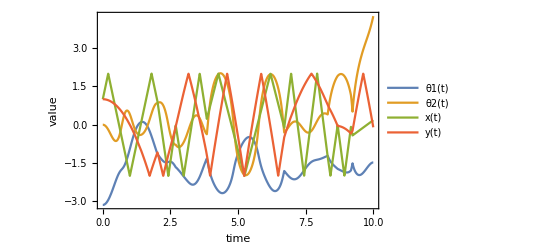

```mathematica
T=10;maxbouncing=100;
ifprint=False;
impactDetectionError=0.01;
intergrationMaxStepSize=0.001;

theta0=-Pi;
theta1=0;
dtheta0=0;
dtheta1=0;

x0=1;
y0=1;
dx0=5;
dy0=0;

{end,data,bounces}=BouncingBall[{theta0,dtheta0,theta1,dtheta1,x0,dx0,y0,dy0}];
plotfigure
plotanimation
```